Linear Duffing oscillator

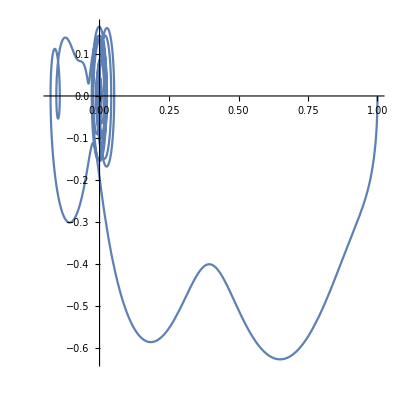

```mathematica
tmax=16;ϵ=0;δ=1;γ=1;T1=1;T2=10;
duffing0=NDSolveValue[{ y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Sin[2 π t/T1]Sin[2 π t/T2],y[0]==1,y'[0]==0},y,{t,0,tmax}];
pl=ParametricPlot[{duffing0[z]/.z->t,D[duffing0[z],z]/.z->t},{t,0,tmax},AspectRatio->1,PlotRange->All]
```

Non linear Duffing oscillator

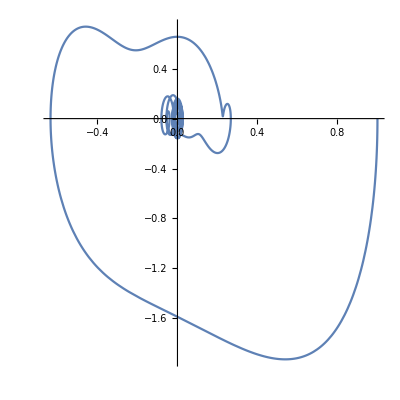

```mathematica
tmax=16;ϵ=10;δ=1;γ=1;T1=1;T2=10;
duffing0=NDSolveValue[{ y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Sin[2 π t/T1]Sin[2 π t/T2],y[0]==1,y'[0]==0},y,{t,0,tmax}];
pnl=ParametricPlot[{duffing0[z]/.z->t,D[duffing0[z],z]/.z->t},{t,0,tmax},AspectRatio->1,PlotRange->All]
```